# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->10,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.995,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.995,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

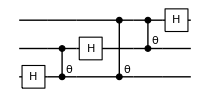

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
```

```mathematica
varMeanInitStates[conf]
```

<|1→{0.400584,0.481403},2→{0.155551,0.0725884},3→{0.74225,0.0363743},4→{0.74225,0.0363743}|>

Compilation with automatically generated ansatz

@cycle1:Mon 5 Sep 2022 05:15:33, fev:325, <E>: 0.3854278237142808 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 1, 5}

@cycle2:Mon 5 Sep 2022 05:16:49, fev:590, <E>: 0.2374890885285207 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 1, 11}

@cycle3:Mon 5 Sep 2022 05:17:32, fev:743, <E>: 0.13520388273351247 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 1, 17}

@cycle4:Mon 5 Sep 2022 05:18:08, fev:882, <E>: 0.11950898402559579 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 22, 0, 1, 20}

@cycle5:Mon 5 Sep 2022 05:19:20, fev:1157, <E>: 0.06704679301891096 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 27, 0, 3, 23}

@cycle6:Mon 5 Sep 2022 05:20:41, fev:1420, <E>: 0.04510425533241946 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 31, 0, 3, 28}

@cycle7:Mon 5 Sep 2022 05:22:06, fev:1662, <E>: 0.03817431527663026 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 37, 0, 3, 40}

@cycle8:Mon 5 Sep 2022 05:23:00, fev:1799, <E>: 0.02247441285977314 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 41, 0, 3, 43}

@cycle9:Mon 5 Sep 2022 05:24:25, fev:2052, <E>: 0.022431599049332063 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 3, 50}

@cycle10:Mon 5 Sep 2022 05:26:01, fev:2316, <E>: 0.02239543193488719 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 50, 0, 3, 56}

I'm slowing down @cycle 11

@cycle11:Mon 5 Sep 2022 05:26:38, fev:2397, <E>: 0.02239543193488719 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 50, 0, 3, 60}

@cycle12:Mon 5 Sep 2022 05:28:52, fev:2738, <E>: 0.021239016477528655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 3, 64}

I'm slowing down @cycle 13

@cycle13:Mon 5 Sep 2022 05:29:51, fev:2832, <E>: 0.021239016477528655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 3, 67}

I'm slowing down @cycle 14

@cycle14:Mon 5 Sep 2022 05:32:41, fev:2932, <E>: 0.021239016477528655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 3, 73}

I'm slowing down @cycle 15

@cycle15:Mon 5 Sep 2022 05:35:15, fev:3025, <E>: 0.021239016477528655 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 60, 0, 3, 82}

compile time:21.1155 minutes; total iterations 3250

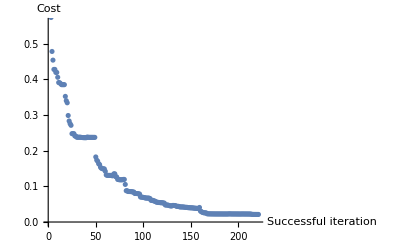

prob(0):<|0→0.332883,1→0.334252,2→0.332866|>

dist_fid=0.115492

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

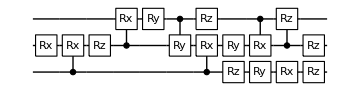

```mathematica
DrawCircuit[ansatz,qubitsnum]
```

```mathematica
θvars
```

<|θ_5→3.93181,θ_6→4.71805,θ_9→-1.60663,θ_14→-2.37532,θ_16→-2.63444,θ_20→-1.55869,θ_23→-1.56739,θ_25→-2.49574,θ_34→-1.24664,θ_42→0.969553,θ_43→-2.68158,θ_45→-1.85846,θ_49→1.06506,θ_64→0.852581,θ_67→-0.325563,θ_83→-0.0341443|>

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
conf["usecorr"]=False;
```

```mathematica
varMeanInitStates[conf]
```

<|1→{0.499845,0.21725},2→{0.400584,0.481403},3→{0.63785,0.117328},4→{0.155551,0.0725884}|>

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

Compilation with automatically generated ansatz

@cycle1:Mon 5 Sep 2022 10:48:20, fev:327, <E>: 0.27648542185718844 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 4, 12}

@cycle2:Mon 5 Sep 2022 10:48:55, fev:650, <E>: 0.17187658896734434 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 5, 18}

@cycle3:Mon 5 Sep 2022 10:49:29, fev:827, <E>: 0.12307780572161761 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 5, 23}

@cycle4:Mon 5 Sep 2022 10:50:07, fev:960, <E>: 0.11142053239730043 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 5, 27}

@cycle5:Mon 5 Sep 2022 10:51:00, fev:1122, <E>: 0.10468014523371248 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 5, 30}

@cycle6:Mon 5 Sep 2022 10:52:00, fev:1276, <E>: 0.10229838024360349 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 5, 33}

@cycle7:Mon 5 Sep 2022 10:52:57, fev:1377, <E>: 0.10134007403186936 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 6, 33}

@cycle8:Mon 5 Sep 2022 10:54:45, fev:1611, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 37}

I'm slowing down @cycle 9

@cycle9:Mon 5 Sep 2022 10:55:02, fev:1639, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 42}

I'm slowing down @cycle 10

@cycle10:Mon 5 Sep 2022 10:55:48, fev:1697, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 51}

@cycle11:Mon 5 Sep 2022 10:59:52, fev:1859, <E>: 0.09690884571505695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 49, 0, 6, 63}

@cycle12:Mon 5 Sep 2022 11:03:35, fev:1984, <E>: 0.09280713302435148 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 67, 0, 6, 82}

@cycle13:Mon 5 Sep 2022 11:07:09, fev:2122, <E>: 0.08987743863421298 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 6, 94}

$Aborted